```mathematica
?Binomial
```

```mathematica
Binomial[24,14]
```

1961256

```mathematica
Binomial[24,9]
```

1307504

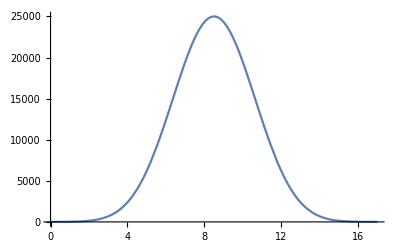

```mathematica
Plot[Binomial[17,x],{x,0,17}]
```

```mathematica
?Sum
```

```mathematica
Sum[Binomial[15+k,5+k],{k,0,10}]
```

7724795

```mathematica
Sum[Binomial[n+k,n-m+k],{k,0,n+m}]
```

1/(1+m)(m Binomial[n,-m+n]-n Binomial[n,-m+n]+Binomial[1+m+2 n,1+2 n]+2 n Binomial[1+m+2 n,1+2 n])

```mathematica
FullSimplify[1/(1+m)(m Binomial[n,-m+n]-n Binomial[n,-m+n]+Binomial[1+m+2 n,1+2 n]+2 n Binomial[1+m+2 n,1+2 n])]
```

((m-n) Binomial[n,-m+n]+(1+2 n) Binomial[1+m+2 n,1+2 n])/(1+m)

```mathematica
DiscretePlot3D[((m-n) Binomial[n,-m+n]+(1+2 n) Binomial[1+m+2 n,1+2 n])/(1+m),{m,1,20},{n,1,20}]
```

-Graphics3D-

```mathematica
Sum[Binomial[10+k,k]-Binomial[10+k,5+k],{k,0,5}]
```

7798